Yohan Lee Lab 4

Example 1 - Left endpoint

```mathematica
Clear[a,b,n]
```

```mathematica
a=3;
```

```mathematica
b=8.5;
```

```mathematica
n=5;
```

```mathematica
width=(b-a)/n;
```

```mathematica
Clear[f];
```

```mathematica
f[x_]:=x^2-3
```

```mathematica
Function[x,x^2-3]
```

Function[x,x^2-3]

```mathematica
width*Sum[f[a+i*width], {i,0,n-1}]
```

145.53

Example 2 - Right endpoint

```mathematica
width*Sum[f[a+(i+1)*width], {i, 0, n-1}]
```

215.105

Example 3 - Midpoint

```mathematica
width*Sum[f[a+(i+1/2)*width], {i, 0, n-1}]
```

178.654

```mathematica
Integrate[f[x], {x, a, b}]
```

179.208

Example 4 - Trapezoid

```mathematica
width*Sum[(f[a+i*width]+f[a+(i+1)*width])/2, {i, 0, n-1}]
```

180.318

Question 1

```mathematica
Clear[a,b,n]
```

```mathematica
a=0;
```

```mathematica
b=5;
```

```mathematica
n=10;
```

```mathematica
width = (b-a)/n;
```

```mathematica
width
```

1/2

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^2
```

```mathematica
Function[x,x^2]
```

Function[x,x^2]

```mathematica
width*Sum[f[a+i*width],{i,0,n-1}]
```

285/8

```mathematica
width*Sum[f[a+i*width],{i,0,n-1}]//N
```

35.625

Question 2

```mathematica
width*Sum[f[a+(i+1)*width], {i,0,n-1}]
```

385/8

```mathematica
width*Sum[f[a+(i+1)*width], {i,0,n-1}]//N
```

48.125

```mathematica
Integrate[f[x], {x,a,b}]
```

125/3

```mathematica
Integrate[f[x], {x,a,b}]//N
```

41.6667

a) Approx 48.125 vs Exact 41.6667
b) The left rectangles underestimate the area. The right rectangles overestimate the area.

Question 3

```mathematica
Clear[f]
```

```mathematica
f[x_]:=Exp[x]*Cos[2*Pi*x]
```

```mathematica
Function[x,Exp[x] Cos[2 π x]]
```

Function[x,Exp[x] Cos[2 π x]]

```mathematica
Clear[a,b,n];
a=0;
b=5;
```

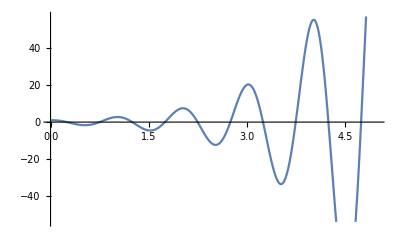

```mathematica
Plot[f[x], {x, 0, 5}]
```

```mathematica
Integrate[f[x], {x,a,b}]
```

(-1+ⅇ^5)/(1+4 π^2)

```mathematica
Integrate[f[x], {x,a,b}]//N
```

3.64177

```mathematica
n=10;
width=(b-a)/n;
width
```

1/2

```mathematica
width*Sum[f[a+(i+1/2)*width], {i, 0, n-1}]//N
```

0.

```mathematica
n=50;
width=(b-a)/n;
width
```

1/10

```mathematica
width*Sum[f[a+(i+1/2)*width], {i, 0, n-1}]//N
```

3.57821

```mathematica
n=100;
width=(b-a)/n;
width
```

1/20

```mathematica
width*Sum[f[a+(i+1/2)*width], {i, 0, n-1}]//N
```

3.62628

```mathematica
n=5;
width=(b-a)/n;
width
```

1

```mathematica
width*Sum[f[a+(i+1/2)*width], {i, 0, n-1}]//N
```

-141.445

a) A small number of intervals will incorporate more negative portions of the function than positive portions.
b) 10% of the exact answer (3.64177) is .364177. We seek an estimate within this error. An estimate with n=23 has error of .34119.

```mathematica
3.64177-.36417
```

3.2776

```mathematica
n=23;
width=(b-a)/n;
width
```

5/23

```mathematica
width*Sum[f[a+(i+1/2)*width], {i, 0, n-1}]//N
```

3.30058

```mathematica
3.64177-3.30058
```

0.34119

Question 4

```mathematica
Clear[a,b,n];
a=0;
b=5;
```

```mathematica
n=10;
width=(b-a)/n;
width
```

1/2

```mathematica
width*Sum[(f[a+i*width]+f[a+(i+1)*width])/2, {i, 0, n-1}]//N
```

9.02606

a) The trapezoid method overestimates the area.

```mathematica
n=23;
width=(b-a)/n;
width
```

5/23

```mathematica
width*Sum[(f[a+i*width]+f[a+(i+1)*width])/2, {i, 0, n-1}]//N
```

4.28007

```mathematica
n=30;
width=(b-a)/n;
width
```

1/6

```mathematica
width*Sum[(f[a+i*width]+f[a+(i+1)*width])/2, {i, 0, n-1}]//N
```

4.00236

b) The estimate must be less than 4.00594 to be within .36417 of 3.64177. This requires requires n=30.

```mathematica
3.64177+.36417
```

4.00594

Question 5

The midpoint method was more accurate as the same choice of n for midpoint will yield a closer answer. The midpoint estimate is less sensitive to the positive a negative fluctuations of the function while the trapezoid is skewed toward the positive values.